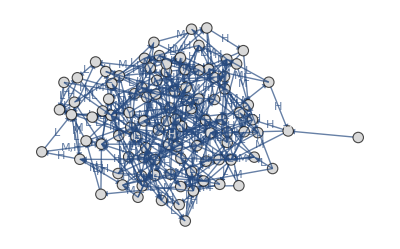

x1.png

```mathematica
SetDirectory[NotebookDirectory[]];
   VertexCircle[{xc_, yc_}, name_, {w_, h_}] := Disk[{xc, yc}, .1];
x1Graph =
   Graph[{100 -> 90 ,
Labeled[0 -> 39, "L"], Labeled[0 -> 18, "M"], Labeled[0 -> 72, "H"], Labeled[1 -> 57, "L"], Labeled[1 -> 52, "M"], Labeled[1 -> 45, "H"], Labeled[2 -> 67, "L"], Labeled[2 -> 53, "M"], Labeled[2 -> 98, "H"], Labeled[3 -> 32, "L"], Labeled[3 -> 96, "M"], Labeled[3 -> 95, "H"], Labeled[4 -> 69, "L"], Labeled[4 -> 57, "M"], Labeled[4 -> 42, "H"], Labeled[5 -> 87, "L"], Labeled[5 -> 4, "M"], Labeled[5 -> 69, "H"], Labeled[6 -> 51, "L"], Labeled[6 -> 18, "M"], Labeled[6 -> 4, "H"], Labeled[7 -> 25, "L"], Labeled[7 -> 77, "M"], Labeled[7 -> 87, "H"], Labeled[8 -> 16, "L"], Labeled[8 -> 77, "M"], Labeled[8 -> 0, "H"], Labeled[9 -> 94, "L"], Labeled[9 -> 37, "M"], Labeled[9 -> 28, "H"], Labeled[10 -> 3, "L"], Labeled[10 -> 87, "M"], Labeled[10 -> 63, "H"], Labeled[11 -> 62, "L"], Labeled[11 -> 6, "M"], Labeled[11 -> 0, "H"], Labeled[12 -> 83, "L,H"], Labeled[12 -> 81, "M"], Labeled[13 -> 56, "L"], Labeled[13 -> 73, "M"], Labeled[13 -> 37, "H"], Labeled[14 -> 36, "L"], Labeled[14 -> 7, "M"], Labeled[14 -> 19, "H"], Labeled[15 -> 10, "L"], Labeled[15 -> 34, "M"], Labeled[15 -> 43, "H"], Labeled[16 -> 21, "L"], Labeled[16 -> 45, "M"], Labeled[16 -> 64, "H"], Labeled[17 -> 94, "L"], Labeled[17 -> 62, "M"], Labeled[17 -> 13, "H"], Labeled[18 -> 96, "L"], Labeled[18 -> 44, "M"], Labeled[18 -> 94, "H"], Labeled[19 -> 75, "L"], Labeled[19 -> 8, "M"], Labeled[19 -> 49, "H"], Labeled[20 -> 88, "L"], Labeled[20 -> 74, "M"], Labeled[20 -> 82, "H"], Labeled[21 -> 52, "L"], Labeled[21 -> 14, "M"], Labeled[21 -> 99, "H"], Labeled[22 -> 18, "L"], Labeled[22 -> 68, "M"], Labeled[22 -> 93, "H"], Labeled[23 -> 25, "L"], Labeled[23 -> 97, "M"], Labeled[23 -> 54, "H"], Labeled[24 -> 22, "L"], Labeled[24 -> 70, "M"], Labeled[24 -> 83, "H"], Labeled[25 -> 99, "L"], Labeled[25 -> 55, "M"], Labeled[25 -> 39, "H"], Labeled[26 -> 14, "L"], Labeled[26 -> 19, "M"], Labeled[26 -> 25, "H"], Labeled[27 -> 76, "L"], Labeled[27 -> 60, "M"], Labeled[27 -> 54, "H"], Labeled[28 -> 86, "L"], Labeled[28 -> 69, "M"], Labeled[28 -> 56, "H"], Labeled[29 -> 83, "L"], Labeled[29 -> 2, "M"], Labeled[29 -> 63, "H"], Labeled[30 -> 76, "L"], Labeled[30 -> 79, "M"], Labeled[30 -> 27, "H"], Labeled[31 -> 77, "L"], Labeled[31 -> 86, "M"], Labeled[31 -> 48, "H"], Labeled[32 -> 63, "L"], Labeled[32 -> 18, "M"], Labeled[32 -> 37, "H"], Labeled[33 -> 8, "L"], Labeled[33 -> 3, "M"], Labeled[33 -> 30, "H"], Labeled[34 -> 30, "L"], Labeled[34 -> 48, "M"], Labeled[34 -> 39, "H"], Labeled[35 -> 72, "L"], Labeled[35 -> 68, "M"], Labeled[35 -> 76, "H"], Labeled[36 -> 8, "L"], Labeled[36 -> 69, "M"], Labeled[36 -> 38, "H"], Labeled[37 -> 48, "L"], Labeled[37 -> 8, "M"], Labeled[37 -> 52, "H"], Labeled[38 -> 29, "L"], Labeled[38 -> 37, "M"], Labeled[38 -> 33, "H"], Labeled[39 -> 89, "L"], Labeled[39 -> 31, "M"], Labeled[39 -> 41, "H"], Labeled[40 -> 78, "L"], Labeled[40 -> 86, "M"], Labeled[40 -> 59, "H"], Labeled[41 -> 62, "L"], Labeled[41 -> 24, "M"], Labeled[41 -> 64, "H"], Labeled[42 -> 97, "L"], Labeled[42 -> 50, "M"], Labeled[42 -> 16, "H"], Labeled[43 -> 85, "L"], Labeled[43 -> 52, "M"], Labeled[43 -> 18, "H"], Labeled[44 -> 46, "L"], Labeled[44 -> 56, "M"], Labeled[44 -> 18, "H"], Labeled[45 -> 51, "L"], Labeled[45 -> 15, "M"], Labeled[45 -> 73, "H"], Labeled[46 -> 41, "L"], Labeled[46 -> 3, "M"], Labeled[46 -> 19, "H"], Labeled[47 -> 63, "L"], Labeled[47 -> 93, "M"], Labeled[47 -> 3, "H"], Labeled[48 -> 69, "L"], Labeled[48 -> 60, "M"], Labeled[48 -> 92, "H"], Labeled[49 -> 71, "L"], Labeled[49 -> 65, "M"], Labeled[49 -> 35, "H"], Labeled[50 -> 97, "L"], Labeled[50 -> 21, "M"], Labeled[50 -> 85, "H"], Labeled[51 -> 61, "L"], Labeled[51 -> 27, "M"], Labeled[51 -> 36, "H"], Labeled[52 -> 20, "L"], Labeled[52 -> 82, "M"], Labeled[52 -> 23, "H"], Labeled[53 -> 0, "L"], Labeled[53 -> 31, "M"], Labeled[53 -> 74, "H"], Labeled[54 -> 38, "L"], Labeled[54 -> 73, "M"], Labeled[54 -> 36, "H"], Labeled[55 -> 60, "L"], Labeled[55 -> 69, "M"], Labeled[55 -> 90, "H"], Labeled[56 -> 75, "L"], Labeled[56 -> 97, "M"], Labeled[56 -> 91, "H"], Labeled[57 -> 14, "L"], Labeled[57 -> 59, "M"], Labeled[57 -> 56, "H"], Labeled[58 -> 94, "L"], Labeled[58 -> 53, "M"], Labeled[58 -> 73, "H"], Labeled[59 -> 19, "L"], Labeled[59 -> 68, "M"], Labeled[59 -> 62, "H"], Labeled[60 -> 1, "L"], Labeled[60 -> 40, "M"], Labeled[60 -> 61, "H"], Labeled[61 -> 46, "L"], Labeled[61 -> 33, "M"], Labeled[61 -> 91, "H"], Labeled[62 -> 30, "L"], Labeled[62 -> 68, "M"], Labeled[62 -> 34, "H"], Labeled[63 -> 18, "L"], Labeled[63 -> 67, "M"], Labeled[63 -> 10, "H"], Labeled[64 -> 18, "L"], Labeled[64 -> 9, "M"], Labeled[64 -> 68, "H"], Labeled[65 -> 35, "L"], Labeled[65 -> 45, "M"], Labeled[65 -> 77, "H"], Labeled[66 -> 91, "L"], Labeled[66 -> 3, "M"], Labeled[66 -> 39, "H"], Labeled[67 -> 3, "L"], Labeled[67 -> 89, "M"], Labeled[67 -> 15, "H"], Labeled[68 -> 19, "L"], Labeled[68 -> 30, "M"], Labeled[68 -> 8, "H"], Labeled[69 -> 27, "L"], Labeled[69 -> 68, "M"], Labeled[69 -> 38, "H"], Labeled[70 -> 26, "L"], Labeled[70 -> 82, "M"], Labeled[70 -> 14, "H"], Labeled[71 -> 35, "L"], Labeled[71 -> 3, "M"], Labeled[71 -> 44, "H"], Labeled[72 -> 64, "L"], Labeled[72 -> 41, "M"], Labeled[72 -> 44, "H"], Labeled[73 -> 51, "L"], Labeled[73 -> 62, "M"], Labeled[73 -> 6, "H"], Labeled[74 -> 61, "L"], Labeled[74 -> 43, "M"], Labeled[74 -> 24, "H"], Labeled[75 -> 7, "L"], Labeled[75 -> 41, "M"], Labeled[75 -> 58, "H"], Labeled[76 -> 58, "L"], Labeled[76 -> 83, "M"], Labeled[76 -> 76, "H"], Labeled[77 -> 8, "L"], Labeled[77 -> 20, "M"], Labeled[77 -> 95, "H"], Labeled[78 -> 62, "L"], Labeled[78 -> 25, "M"], Labeled[78 -> 61, "H"], Labeled[79 -> 0, "L"], Labeled[79 -> 31, "M"], Labeled[79 -> 2, "H"], Labeled[80 -> 86, "L"], Labeled[80 -> 53, "M"], Labeled[80 -> 99, "H"], Labeled[81 -> 82, "L"], Labeled[81 -> 67, "M"], Labeled[81 -> 93, "H"], Labeled[82 -> 16, "L"], Labeled[82 -> 37, "M"], Labeled[82 -> 83, "H"], Labeled[83 -> 20, "L"], Labeled[83 -> 7, "M"], Labeled[83 -> 81, "H"], Labeled[84 -> 26, "L"], Labeled[84 -> 44, "M"], Labeled[84 -> 97, "H"], Labeled[85 -> 93, "L"], Labeled[85 -> 40, "M"], Labeled[85 -> 73, "H"], Labeled[86 -> 51, "L"], Labeled[86 -> 7, "M"], Labeled[86 -> 27, "H"], Labeled[87 -> 36, "L"], Labeled[87 -> 65, "M"], Labeled[87 -> 62, "H"], Labeled[88 -> 34, "L"], Labeled[88 -> 67, "M"], Labeled[88 -> 73, "H"], Labeled[89 -> 50, "L"], Labeled[89 -> 71, "M"], Labeled[89 -> 95, "H"], Labeled[90 -> 62, "L"], Labeled[90 -> 19, "M"], Labeled[90 -> 59, "H"], Labeled[91 -> 54, "L"], Labeled[91 -> 60, "M"], Labeled[91 -> 25, "H"], Labeled[92 -> 28, "L"], Labeled[92 -> 70, "M"], Labeled[92 -> 62, "H"], Labeled[93 -> 5, "L"], Labeled[93 -> 14, "M"], Labeled[93 -> 57, "H"], Labeled[94 -> 12, "L"], Labeled[94 -> 44, "M"], Labeled[94 -> 78, "H"], Labeled[95 -> 5, "L"], Labeled[95 -> 83, "M"], Labeled[95 -> 85, "H"], Labeled[96 -> 86, "L,M"], Labeled[96 -> 18, "H"], Labeled[97 -> 92, "L,H"], Labeled[97 -> 31, "M"], Labeled[98 -> 67, "L"], Labeled[98 -> 83, "M,H"], Labeled[99 -> 25, "L"], Labeled[99 -> 76, "M"], Labeled[99 -> 2, "H"]     },
   EdgeShapeFunction -> 
    GraphElementData["EdgeShapeFunction", "FilledArrow"],
   VertexStyle -> LightGray,
   VertexShapeFunction -> VertexCircle,
   VertexLabels -> {0 -> Placed["L", Center], 1 -> Placed["M", Center], 2 -> Placed["M", Center], 3 -> Placed["L", Center], 4 -> Placed["M", Center], 5 -> Placed["H", Center], 6 -> Placed["L", Center], 7 -> Placed["H", Center], 8 -> Placed["L", Center], 9 -> Placed["H", Center], 10 -> Placed["H", Center], 11 -> Placed["M", Center], 12 -> Placed["L", Center], 13 -> Placed["L", Center], 14 -> Placed["H", Center], 15 -> Placed["H", Center], 16 -> Placed["M", Center], 17 -> Placed["L", Center], 18 -> Placed["L", Center], 19 -> Placed["H", Center], 20 -> Placed["M", Center], 21 -> Placed["M", Center], 22 -> Placed["M", Center], 23 -> Placed["L", Center], 24 -> Placed["L", Center], 25 -> Placed["H", Center], 26 -> Placed["L", Center], 27 -> Placed["M", Center], 28 -> Placed["M", Center], 29 -> Placed["L", Center], 30 -> Placed["H", Center], 31 -> Placed["M", Center], 32 -> Placed["M", Center], 33 -> Placed["L", Center], 34 -> Placed["H", Center], 35 -> Placed["L", Center], 36 -> Placed["L", Center], 37 -> Placed["M", Center], 38 -> Placed["L", Center], 39 -> Placed["H", Center], 40 -> Placed["H", Center], 41 -> Placed["L", Center], 42 -> Placed["M", Center], 43 -> Placed["H", Center], 44 -> Placed["H", Center], 45 -> Placed["M", Center], 46 -> Placed["L", Center], 47 -> Placed["M", Center], 48 -> Placed["L", Center], 49 -> Placed["L", Center], 50 -> Placed["H", Center], 51 -> Placed["L", Center], 52 -> Placed["M", Center], 53 -> Placed["L", Center], 54 -> Placed["L", Center], 55 -> Placed["H", Center], 56 -> Placed["H", Center], 57 -> Placed["L", Center], 58 -> Placed["M", Center], 59 -> Placed["M", Center], 60 -> Placed["H", Center], 61 -> Placed["M", Center], 62 -> Placed["H", Center], 63 -> Placed["H", Center], 64 -> Placed["H", Center], 65 -> Placed["L", Center], 66 -> Placed["H", Center], 67 -> Placed["H", Center], 68 -> Placed["M", Center], 69 -> Placed["H", Center], 70 -> Placed["L", Center], 71 -> Placed["M", Center], 72 -> Placed["L", Center], 73 -> Placed["M", Center], 74 -> Placed["M", Center], 75 -> Placed["H", Center], 76 -> Placed["M", Center], 77 -> Placed["H", Center], 78 -> Placed["L", Center], 79 -> Placed["H", Center], 80 -> Placed["L", Center], 81 -> Placed["H", Center], 82 -> Placed["L", Center], 83 -> Placed["M", Center], 84 -> Placed["L", Center], 85 -> Placed["H", Center], 86 -> Placed["L", Center], 87 -> Placed["M", Center], 88 -> Placed["L", Center], 89 -> Placed["H", Center], 90 -> Placed["M", Center], 91 -> Placed["M", Center], 92 -> Placed["H", Center], 93 -> Placed["H", Center], 94 -> Placed["L", Center], 95 -> Placed["M", Center], 96 -> Placed["L", Center], 97 -> Placed["L", Center], 98 -> Placed["L", Center], 99 -> Placed["H", Center]}
   ];
S = Show[x1Graph]
Export["x1.png",S]
```

```mathematica
ConnectedComponents[x1Graph]
```

{{90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,62,12,83,81,56,73,14,36,19,15,34,43,21,64,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,92,71,65,61,91,58},{100},{11},{13},{17},{47},{66},{80},{84}}

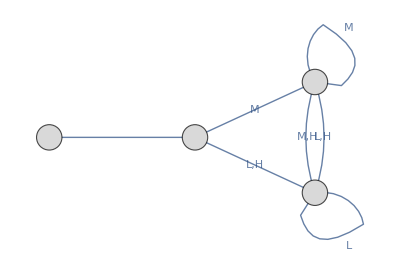

```mathematica
SetDirectory[NotebookDirectory[]];
   VertexCircle[{xc_, yc_}, name_, {w_, h_}] := Disk[{xc, yc}, .1];
x0Graph =
   Graph[{3 -> 2 ,
Labeled[0 -> 1, "L,H"], Labeled[0 -> 0, "M"], Labeled[1 -> 1, "L"], Labeled[1 -> 0, "M,H"], Labeled[2 -> 1, "L,H"], Labeled[2 -> 0, "M"]     },
   EdgeShapeFunction -> 
    GraphElementData["EdgeShapeFunction", "FilledArrow"],
   VertexStyle -> LightGray,
   VertexShapeFunction -> VertexCircle,
   VertexLabels -> {0 -> Placed["H", Center], 1 -> Placed["H", Center], 2 -> Placed["L", Center]}
   ];
S = Show[x0Graph]
(*Export["x0.png",S]*)
```

```mathematica
ConnectedComponents[x0Graph]
```

{{0,1},{2},{3}}

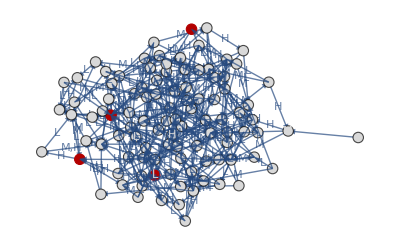

```mathematica
HighlightGraph[x1Graph,%]
```

```mathematica
WeaklyConnectedComponents[x1Graph]
```

{{100,90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,11,62,12,83,81,13,56,73,14,36,19,15,34,43,21,64,17,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,47,92,71,65,61,91,58,66,80,84}}

```mathematica
HighlightGraph[x1Graph,Subgraph[x1Graph,#]&/@%]
```

-Graphics-

```mathematica
KCoreComponents[x1Graph,90]
```

{}

```mathematica
HighlightGraph[Graph[{100,90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,11,62,12,83,81,13,56,73,14,36,19,15,34,43,21,64,17,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,47,92,71,65,61,91,58,66,80,84},{{{1,2},{3,4},{3,5},{3,6},{7,8},{7,9},{7,10},{11,12},{11,13},{11,14},{15,16},{15,17},{15,18},{19,20},{19,8},{19,21},{22,23},{22,19},{22,20},{24,25},{24,5},{24,19},{26,27},{26,28},{26,23},{29,30},{29,28},{29,3},{31,32},{31,33},{31,34},{35,15},{35,23},{35,36},{37,38},{37,24},{37,3},{39,40},{39,41},{42,43},{42,44},{42,33},{45,46},{45,26},{45,47},{48,35},{48,49},{48,50},{30,51},{30,10},{30,52},{53,32},{53,38},{53,42},{5,17},{5,54},{5,32},{47,55},{47,29},{47,56},{57,58},{57,59},{57,60},{51,9},{51,45},{51,61},{62,5},{62,63},{62,64},{65,27},{65,66},{65,67},{68,62},{68,69},{68,40},{27,61},{27,70},{27,4},{71,45},{71,47},{71,27},{72,73},{72,74},{72,67},{34,75},{34,20},{34,43},{76,40},{76,11},{76,36},{77,73},{77,78},{77,72},{79,28},{79,75},{79,80},{16,36},{16,5},{16,33},{81,29},{81,15},{81,77},{49,77},{49,80},{49,4},{82,6},{82,63},{82,73},{46,29},{46,20},{46,83},{33,80},{33,29},{33,9},{83,76},{83,33},{83,81},{4,84},{4,79},{4,85},{86,87},{86,75},{86,88},{85,38},{85,68},{85,52},{21,66},{21,89},{21,30},{50,90},{50,9},{50,5},{54,91},{54,43},{54,5},{10,25},{10,48},{10,44},{91,85},{91,15},{91,47},{92,36},{92,64},{92,15},{80,20},{80,74},{80,93},{56,94},{56,95},{56,82},{89,66},{89,51},{89,90},{25,96},{25,72},{25,46},{9,57},{9,60},{9,65},{13,3},{13,79},{13,59},{67,83},{67,44},{67,46},{70,74},{70,20},{70,2},{43,55},{43,66},{43,97},{8,45},{8,88},{8,43},{98,32},{98,13},{98,44},{88,47},{88,63},{88,38},{74,7},{74,86},{74,96},{96,91},{96,81},{96,97},{38,77},{38,63},{38,49},{36,5},{36,12},{36,35},{52,5},{52,31},{52,63},{95,82},{95,10},{95,28},{99,97},{99,15},{99,4},{12,15},{12,84},{12,48},{63,47},{63,77},{63,29},{20,72},{20,63},{20,83},{69,71},{69,60},{69,45},{94,82},{94,15},{94,54},{6,52},{6,85},{6,54},{44,25},{44,38},{44,24},{59,96},{59,50},{59,68},{55,26},{55,85},{55,98},{73,98},{73,40},{73,73},{28,29},{28,57},{28,18},{87,38},{87,27},{87,96},{78,3},{78,79},{78,11},{100,75},{100,13},{100,61},{41,60},{41,12},{41,64},{60,30},{60,33},{60,40},{40,57},{40,26},{40,41},{101,71},{101,54},{101,66},{90,64},{90,86},{90,44},{75,25},{75,26},{75,72},{23,46},{23,95},{23,38},{58,49},{58,12},{58,44},{84,89},{84,94},{84,18},{2,38},{2,47},{2,88},{97,67},{97,74},{97,27},{93,34},{93,69},{93,38},{64,22},{64,45},{64,8},{32,39},{32,54},{32,87},{18,22},{18,40},{18,90},{17,75},{17,5},{66,93},{66,79},{14,12},{14,40},{61,27},{61,73},{61,11}},Null},{EdgeLabels->{94->12->"L",83->81->"H",69->27->"L",35->72->"L",11->62->"L",62->34->"H",92->62->"H",66->39->"H",10->87->"M",80->53->"M",14->19->"H",29->2->"M",99->25->"L",1->52->"M",10->3->"L",73->62->"M",72->44->"H",56->97->"M",88->67->"M",16->45->"M",7->87->"H",28->86->"L",4->69->"L",64->68->"H",13->73->"M",19->75->"L",7->77->"M",24->70->"M",65->45->"M",76->83->"M",72->64->"L",31->48->"H",95->83->"M",55->90->"H",38->33->"H",76->76->"H",69->68->"M",68->19->"L",98->67->"L",99->2->"H",87->62->"H",46->41->"L",8->77->"M",47->63->"L",31->77->"L",51->61->"L",24->83->"H",12->81->"M",27->76->"L",98->83->"M,H",26->14->"L",14->36->"L",59->19->"L",25->99->"L",26->25->"H",35->68->"M",82->37->"M",62->68->"M",17->94->"L",55->60->"L",57->59->"M",19->8->"M",83->20->"L",21->99->"H",45->15->"M",68->8->"H",61->91->"H",59->62->"H",36->8->"L",0->72->"H",68->30->"M",3->96->"M",26->19->"M",99->76->"M",0->18->"M",9->28->"H",85->73->"H",16->64->"H",75->7->"L",95->85->"H",54->36->"H",40->59->"H",5->87->"L",60->1->"L",97->31->"M",86->27->"H",72->41->"M",64->9->"M",48->69->"L",41->24->"M",71->35->"L",58->73->"H",21->52->"L",18->96->"L",50->21->"M",86->7->"M",76->58->"L",84->26->"L",33->3->"M",9->37->"M",27->60->"M",91->54->"L",6->18->"M",40->78->"L",54->38->"L",96->18->"H",47->93->"M",52->82->"M",70->82->"M",53->31->"M",49->65->"M",5->4->"M",36->38->"H",15->10->"L",22->93->"H",44->18->"H",60->40->"M",55->69->"M",75->41->"M",86->51->"L",85->40->"M",10->63->"H",94->44->"M",88->34->"L",41->62->"L",58->94->"L",48->92->"H",81->93->"H",18->44->"M",93->57->"H",58->53->"M",92->70->"M",63->18->"L",79->0->"L",1->45->"H",73->6->"H",34->30->"L",34->39->"H",43->85->"L",90->62->"L",37->48->"L",23->54->"H",42->97->"L",15->43->"H",74->24->"H",38->29->"L",33->30->"H",34->48->"M",79->31->"M",28->56->"H",67->15->"H",13->37->"H",2->53->"M",18->94->"H",90->59->"H",93->5->"L",52->20->"L",64->18->"L",79->2->"H",69->38->"H",87->36->"L",56->91->"H",14->7->"M",24->22->"L",61->33->"M",50->97->"L",27->54->"H",43->52->"M",91->60->"M",0->39->"L",49->71->"L",11->0->"H",67->3->"L",44->56->"M",82->16->"L",67->89->"M",35->76->"H",66->91->"L",89->71->"M",2->67->"L",38->37->"M",45->73->"H",46->3->"M",94->78->"H",43->18->"H",59->68->"M",47->3->"H",71->44->"H",37->8->"M",30->27->"H",23->25->"L",96->86->"L,M",7->25->"L",12->83->"L,H",70->26->"L",65->77->"H",92->28->"L",74->43->"M",77->95->"H",80->86->"L",42->50->"M",51->27->"M",32->63->"L",13->56->"L",22->68->"M",17->62->"M",77->8->"L",39->31->"M",56->75->"L",74->61->"L",25->55->"M",70->14->"H",89->95->"H",8->0->"H",81->82->"L",37->52->"H",87->65->"M",22->18->"L",20->74->"M",6->51->"L",5->69->"H",44->46->"L",28->69->"M",95->5->"L",40->86->"M",73->51->"L",21->14->"M",4->42->"H",49->35->"H",50->85->"H",32->18->"M",9->94->"L",62->30->"L",23->97->"M",82->83->"H",48->60->"M",2->98->"H",97->92->"L,H",75->58->"H",41->64->"H",78->61->"H",91->25->"H",15->34->"M",57->56->"H",3->32->"L",20->88->"L",6->4->"H",17->13->"H",60->61->"H",31->86->"M",45->51->"L",25->39->"H",80->99->"H",1->57->"L",36->69->"M",30->79->"M",77->20->"M",63->67->"M",83->7->"M",51->36->"H",39->41->"H",42->16->"H",54->73->"M",65->35->"L",93->14->"M",78->25->"M",61->46->"L",90->19->"M",89->50->"L",20->82->"H",53->74->"H",85->93->"L",3->95->"H",29->63->"H",84->97->"H",81->67->"M",8->16->"L",53->0->"L",33->8->"L",32->37->"H",29->83->"L",52->23->"H",19->49->"H",46->19->"H",88->73->"H",30->76->"L",66->3->"M",78->62->"L",11->6->"M",71->3->"M",16->21->"L",4->57->"M",84->44->"M",39->89->"L",63->10->"H",57->14->"L"},EdgeShapeFunction->{"ShortFilledArrow"},VertexLabels->{70->Placed["L",Center],68->Placed["M",Center],93->Placed["H",Center],59->Placed["M",Center],13->Placed["L",Center],18->Placed["L",Center],47->Placed["M",Center],88->Placed["L",Center],6->Placed["L",Center],20->Placed["M",Center],81->Placed["H",Center],17->Placed["L",Center],82->Placed["L",Center],53->Placed["L",Center],51->Placed["L",Center],46->Placed["L",Center],39->Placed["H",Center],23->Placed["L",Center],97->Placed["L",Center],24->Placed["L",Center],12->Placed["L",Center],54->Placed["L",Center],25->Placed["H",Center],80->Placed["L",Center],87->Placed["M",Center],31->Placed["M",Center],64->Placed["H",Center],29->Placed["L",Center],91->Placed["M",Center],95->Placed["M",Center],94->Placed["L",Center],89->Placed["H",Center],96->Placed["L",Center],77->Placed["H",Center],45->Placed["M",Center],3->Placed["L",Center],55->Placed["H",Center],32->Placed["M",Center],84->Placed["L",Center],75->Placed["H",Center],92->Placed["H",Center],73->Placed["M",Center],22->Placed["M",Center],19->Placed["H",Center],90->Placed["M",Center],21->Placed["M",Center],35->Placed["L",Center],58->Placed["M",Center],38->Placed["L",Center],78->Placed["L",Center],61->Placed["M",Center],72->Placed["L",Center],60->Placed["H",Center],0->Placed["L",Center],48->Placed["L",Center],41->Placed["L",Center],85->Placed["H",Center],63->Placed["H",Center],5->Placed["H",Center],28->Placed["M",Center],9->Placed["H",Center],86->Placed["L",Center],49->Placed["L",Center],30->Placed["H",Center],44->Placed["H",Center],36->Placed["L",Center],76->Placed["M",Center],67->Placed["H",Center],98->Placed["L",Center],2->Placed["M",Center],27->Placed["M",Center],65->Placed["L",Center],42->Placed["M",Center],26->Placed["L",Center],37->Placed["M",Center],8->Placed["L",Center],83->Placed["M",Center],71->Placed["M",Center],50->Placed["H",Center],15->Placed["H",Center],4->Placed["M",Center],11->Placed["M",Center],7->Placed["H",Center],66->Placed["H",Center],34->Placed["H",Center],74->Placed["M",Center],16->Placed["M",Center],69->Placed["H",Center],43->Placed["H",Center],1->Placed["M",Center],14->Placed["H",Center],56->Placed["H",Center],99->Placed["H",Center],62->Placed["H",Center],40->Placed["H",Center],79->Placed["H",Center],52->Placed["M",Center],10->Placed["H",Center],57->Placed["L",Center],33->Placed["L",Center]},VertexShapeFunction->{VertexCircle},VertexStyle->{GrayLevel[0.85]}}],(Subgraph[Graph[{100,90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,11,62,12,83,81,13,56,73,14,36,19,15,34,43,21,64,17,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,47,92,71,65,61,91,58,66,80,84},{{{1,2},{3,4},{3,5},{3,6},{7,8},{7,9},{7,10},{11,12},{11,13},{11,14},{15,16},{15,17},{15,18},{19,20},{19,8},{19,21},{22,23},{22,19},{22,20},{24,25},{24,5},{24,19},{26,27},{26,28},{26,23},{29,30},{29,28},{29,3},{31,32},{31,33},{31,34},{35,15},{35,23},{35,36},{37,38},{37,24},{37,3},{39,40},{39,41},{42,43},{42,44},{42,33},{45,46},{45,26},{45,47},{48,35},{48,49},{48,50},{30,51},{30,10},{30,52},{53,32},{53,38},{53,42},{5,17},{5,54},{5,32},{47,55},{47,29},{47,56},{57,58},{57,59},{57,60},{51,9},{51,45},{51,61},{62,5},{62,63},{62,64},{65,27},{65,66},{65,67},{68,62},{68,69},{68,40},{27,61},{27,70},{27,4},{71,45},{71,47},{71,27},{72,73},{72,74},{72,67},{34,75},{34,20},{34,43},{76,40},{76,11},{76,36},{77,73},{77,78},{77,72},{79,28},{79,75},{79,80},{16,36},{16,5},{16,33},{81,29},{81,15},{81,77},{49,77},{49,80},{49,4},{82,6},{82,63},{82,73},{46,29},{46,20},{46,83},{33,80},{33,29},{33,9},{83,76},{83,33},{83,81},{4,84},{4,79},{4,85},{86,87},{86,75},{86,88},{85,38},{85,68},{85,52},{21,66},{21,89},{21,30},{50,90},{50,9},{50,5},{54,91},{54,43},{54,5},{10,25},{10,48},{10,44},{91,85},{91,15},{91,47},{92,36},{92,64},{92,15},{80,20},{80,74},{80,93},{56,94},{56,95},{56,82},{89,66},{89,51},{89,90},{25,96},{25,72},{25,46},{9,57},{9,60},{9,65},{13,3},{13,79},{13,59},{67,83},{67,44},{67,46},{70,74},{70,20},{70,2},{43,55},{43,66},{43,97},{8,45},{8,88},{8,43},{98,32},{98,13},{98,44},{88,47},{88,63},{88,38},{74,7},{74,86},{74,96},{96,91},{96,81},{96,97},{38,77},{38,63},{38,49},{36,5},{36,12},{36,35},{52,5},{52,31},{52,63},{95,82},{95,10},{95,28},{99,97},{99,15},{99,4},{12,15},{12,84},{12,48},{63,47},{63,77},{63,29},{20,72},{20,63},{20,83},{69,71},{69,60},{69,45},{94,82},{94,15},{94,54},{6,52},{6,85},{6,54},{44,25},{44,38},{44,24},{59,96},{59,50},{59,68},{55,26},{55,85},{55,98},{73,98},{73,40},{73,73},{28,29},{28,57},{28,18},{87,38},{87,27},{87,96},{78,3},{78,79},{78,11},{100,75},{100,13},{100,61},{41,60},{41,12},{41,64},{60,30},{60,33},{60,40},{40,57},{40,26},{40,41},{101,71},{101,54},{101,66},{90,64},{90,86},{90,44},{75,25},{75,26},{75,72},{23,46},{23,95},{23,38},{58,49},{58,12},{58,44},{84,89},{84,94},{84,18},{2,38},{2,47},{2,88},{97,67},{97,74},{97,27},{93,34},{93,69},{93,38},{64,22},{64,45},{64,8},{32,39},{32,54},{32,87},{18,22},{18,40},{18,90},{17,75},{17,5},{66,93},{66,79},{14,12},{14,40},{61,27},{61,73},{61,11}},Null},{EdgeLabels->{94->12->"L",83->81->"H",69->27->"L",35->72->"L",11->62->"L",62->34->"H",92->62->"H",66->39->"H",10->87->"M",80->53->"M",14->19->"H",29->2->"M",99->25->"L",1->52->"M",10->3->"L",73->62->"M",72->44->"H",56->97->"M",88->67->"M",16->45->"M",7->87->"H",28->86->"L",4->69->"L",64->68->"H",13->73->"M",19->75->"L",7->77->"M",24->70->"M",65->45->"M",76->83->"M",72->64->"L",31->48->"H",95->83->"M",55->90->"H",38->33->"H",76->76->"H",69->68->"M",68->19->"L",98->67->"L",99->2->"H",87->62->"H",46->41->"L",8->77->"M",47->63->"L",31->77->"L",51->61->"L",24->83->"H",12->81->"M",27->76->"L",98->83->"M,H",26->14->"L",14->36->"L",59->19->"L",25->99->"L",26->25->"H",35->68->"M",82->37->"M",62->68->"M",17->94->"L",55->60->"L",57->59->"M",19->8->"M",83->20->"L",21->99->"H",45->15->"M",68->8->"H",61->91->"H",59->62->"H",36->8->"L",0->72->"H",68->30->"M",3->96->"M",26->19->"M",99->76->"M",0->18->"M",9->28->"H",85->73->"H",16->64->"H",75->7->"L",95->85->"H",54->36->"H",40->59->"H",5->87->"L",60->1->"L",97->31->"M",86->27->"H",72->41->"M",64->9->"M",48->69->"L",41->24->"M",71->35->"L",58->73->"H",21->52->"L",18->96->"L",50->21->"M",86->7->"M",76->58->"L",84->26->"L",33->3->"M",9->37->"M",27->60->"M",91->54->"L",6->18->"M",40->78->"L",54->38->"L",96->18->"H",47->93->"M",52->82->"M",70->82->"M",53->31->"M",49->65->"M",5->4->"M",36->38->"H",15->10->"L",22->93->"H",44->18->"H",60->40->"M",55->69->"M",75->41->"M",86->51->"L",85->40->"M",10->63->"H",94->44->"M",88->34->"L",41->62->"L",58->94->"L",48->92->"H",81->93->"H",18->44->"M",93->57->"H",58->53->"M",92->70->"M",63->18->"L",79->0->"L",1->45->"H",73->6->"H",34->30->"L",34->39->"H",43->85->"L",90->62->"L",37->48->"L",23->54->"H",42->97->"L",15->43->"H",74->24->"H",38->29->"L",33->30->"H",34->48->"M",79->31->"M",28->56->"H",67->15->"H",13->37->"H",2->53->"M",18->94->"H",90->59->"H",93->5->"L",52->20->"L",64->18->"L",79->2->"H",69->38->"H",87->36->"L",56->91->"H",14->7->"M",24->22->"L",61->33->"M",50->97->"L",27->54->"H",43->52->"M",91->60->"M",0->39->"L",49->71->"L",11->0->"H",67->3->"L",44->56->"M",82->16->"L",67->89->"M",35->76->"H",66->91->"L",89->71->"M",2->67->"L",38->37->"M",45->73->"H",46->3->"M",94->78->"H",43->18->"H",59->68->"M",47->3->"H",71->44->"H",37->8->"M",30->27->"H",23->25->"L",96->86->"L,M",7->25->"L",12->83->"L,H",70->26->"L",65->77->"H",92->28->"L",74->43->"M",77->95->"H",80->86->"L",42->50->"M",51->27->"M",32->63->"L",13->56->"L",22->68->"M",17->62->"M",77->8->"L",39->31->"M",56->75->"L",74->61->"L",25->55->"M",70->14->"H",89->95->"H",8->0->"H",81->82->"L",37->52->"H",87->65->"M",22->18->"L",20->74->"M",6->51->"L",5->69->"H",44->46->"L",28->69->"M",95->5->"L",40->86->"M",73->51->"L",21->14->"M",4->42->"H",49->35->"H",50->85->"H",32->18->"M",9->94->"L",62->30->"L",23->97->"M",82->83->"H",48->60->"M",2->98->"H",97->92->"L,H",75->58->"H",41->64->"H",78->61->"H",91->25->"H",15->34->"M",57->56->"H",3->32->"L",20->88->"L",6->4->"H",17->13->"H",60->61->"H",31->86->"M",45->51->"L",25->39->"H",80->99->"H",1->57->"L",36->69->"M",30->79->"M",77->20->"M",63->67->"M",83->7->"M",51->36->"H",39->41->"H",42->16->"H",54->73->"M",65->35->"L",93->14->"M",78->25->"M",61->46->"L",90->19->"M",89->50->"L",20->82->"H",53->74->"H",85->93->"L",3->95->"H",29->63->"H",84->97->"H",81->67->"M",8->16->"L",53->0->"L",33->8->"L",32->37->"H",29->83->"L",52->23->"H",19->49->"H",46->19->"H",88->73->"H",30->76->"L",66->3->"M",78->62->"L",11->6->"M",71->3->"M",16->21->"L",4->57->"M",84->44->"M",39->89->"L",63->10->"H",57->14->"L"},EdgeShapeFunction->{"ShortFilledArrow"},VertexLabels->{70->Placed["L",Center],68->Placed["M",Center],93->Placed["H",Center],59->Placed["M",Center],13->Placed["L",Center],18->Placed["L",Center],47->Placed["M",Center],88->Placed["L",Center],6->Placed["L",Center],20->Placed["M",Center],81->Placed["H",Center],17->Placed["L",Center],82->Placed["L",Center],53->Placed["L",Center],51->Placed["L",Center],46->Placed["L",Center],39->Placed["H",Center],23->Placed["L",Center],97->Placed["L",Center],24->Placed["L",Center],12->Placed["L",Center],54->Placed["L",Center],25->Placed["H",Center],80->Placed["L",Center],87->Placed["M",Center],31->Placed["M",Center],64->Placed["H",Center],29->Placed["L",Center],91->Placed["M",Center],95->Placed["M",Center],94->Placed["L",Center],89->Placed["H",Center],96->Placed["L",Center],77->Placed["H",Center],45->Placed["M",Center],3->Placed["L",Center],55->Placed["H",Center],32->Placed["M",Center],84->Placed["L",Center],75->Placed["H",Center],92->Placed["H",Center],73->Placed["M",Center],22->Placed["M",Center],19->Placed["H",Center],90->Placed["M",Center],21->Placed["M",Center],35->Placed["L",Center],58->Placed["M",Center],38->Placed["L",Center],78->Placed["L",Center],61->Placed["M",Center],72->Placed["L",Center],60->Placed["H",Center],0->Placed["L",Center],48->Placed["L",Center],41->Placed["L",Center],85->Placed["H",Center],63->Placed["H",Center],5->Placed["H",Center],28->Placed["M",Center],9->Placed["H",Center],86->Placed["L",Center],49->Placed["L",Center],30->Placed["H",Center],44->Placed["H",Center],36->Placed["L",Center],76->Placed["M",Center],67->Placed["H",Center],98->Placed["L",Center],2->Placed["M",Center],27->Placed["M",Center],65->Placed["L",Center],42->Placed["M",Center],26->Placed["L",Center],37->Placed["M",Center],8->Placed["L",Center],83->Placed["M",Center],71->Placed["M",Center],50->Placed["H",Center],15->Placed["H",Center],4->Placed["M",Center],11->Placed["M",Center],7->Placed["H",Center],66->Placed["H",Center],34->Placed["H",Center],74->Placed["M",Center],16->Placed["M",Center],69->Placed["H",Center],43->Placed["H",Center],1->Placed["M",Center],14->Placed["H",Center],56->Placed["H",Center],99->Placed["H",Center],62->Placed["H",Center],40->Placed["H",Center],79->Placed["H",Center],52->Placed["M",Center],10->Placed["H",Center],57->Placed["L",Center],33->Placed["L",Center]},VertexShapeFunction->{VertexCircle},VertexStyle->{GrayLevel[0.85]}}],#1]&)/@{}]
```

-Graphics-

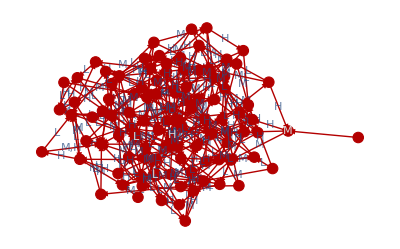

```mathematica
HighlightGraph[x1Graph,Subgraph[x1Graph,%]]
```

```mathematica
ConnectedGraphQ[x0Graph]
```

False

```mathematica
x0Graph
```

-Graphics-

```mathematica
ConnectedGraphQ[x0Graph]
```

False

```mathematica
FindMinimumCut[x0Graph]
```

{0,{{0,1},{3,2}}}

```mathematica
ConnectedComponents[x1Graph]
```

{{90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,62,12,83,81,56,73,14,36,19,15,34,43,21,64,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,92,71,65,61,91,58},{100},{11},{13},{17},{47},{66},{80},{84}}

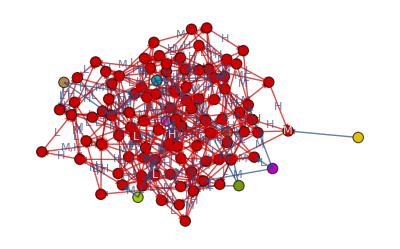

```mathematica
HighlightGraph[Graph[{100,90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,11,62,12,83,81,13,56,73,14,36,19,15,34,43,21,64,17,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,47,92,71,65,61,91,58,66,80,84},{{{1,2},{3,4},{3,5},{3,6},{7,8},{7,9},{7,10},{11,12},{11,13},{11,14},{15,16},{15,17},{15,18},{19,20},{19,8},{19,21},{22,23},{22,19},{22,20},{24,25},{24,5},{24,19},{26,27},{26,28},{26,23},{29,30},{29,28},{29,3},{31,32},{31,33},{31,34},{35,15},{35,23},{35,36},{37,38},{37,24},{37,3},{39,40},{39,41},{42,43},{42,44},{42,33},{45,46},{45,26},{45,47},{48,35},{48,49},{48,50},{30,51},{30,10},{30,52},{53,32},{53,38},{53,42},{5,17},{5,54},{5,32},{47,55},{47,29},{47,56},{57,58},{57,59},{57,60},{51,9},{51,45},{51,61},{62,5},{62,63},{62,64},{65,27},{65,66},{65,67},{68,62},{68,69},{68,40},{27,61},{27,70},{27,4},{71,45},{71,47},{71,27},{72,73},{72,74},{72,67},{34,75},{34,20},{34,43},{76,40},{76,11},{76,36},{77,73},{77,78},{77,72},{79,28},{79,75},{79,80},{16,36},{16,5},{16,33},{81,29},{81,15},{81,77},{49,77},{49,80},{49,4},{82,6},{82,63},{82,73},{46,29},{46,20},{46,83},{33,80},{33,29},{33,9},{83,76},{83,33},{83,81},{4,84},{4,79},{4,85},{86,87},{86,75},{86,88},{85,38},{85,68},{85,52},{21,66},{21,89},{21,30},{50,90},{50,9},{50,5},{54,91},{54,43},{54,5},{10,25},{10,48},{10,44},{91,85},{91,15},{91,47},{92,36},{92,64},{92,15},{80,20},{80,74},{80,93},{56,94},{56,95},{56,82},{89,66},{89,51},{89,90},{25,96},{25,72},{25,46},{9,57},{9,60},{9,65},{13,3},{13,79},{13,59},{67,83},{67,44},{67,46},{70,74},{70,20},{70,2},{43,55},{43,66},{43,97},{8,45},{8,88},{8,43},{98,32},{98,13},{98,44},{88,47},{88,63},{88,38},{74,7},{74,86},{74,96},{96,91},{96,81},{96,97},{38,77},{38,63},{38,49},{36,5},{36,12},{36,35},{52,5},{52,31},{52,63},{95,82},{95,10},{95,28},{99,97},{99,15},{99,4},{12,15},{12,84},{12,48},{63,47},{63,77},{63,29},{20,72},{20,63},{20,83},{69,71},{69,60},{69,45},{94,82},{94,15},{94,54},{6,52},{6,85},{6,54},{44,25},{44,38},{44,24},{59,96},{59,50},{59,68},{55,26},{55,85},{55,98},{73,98},{73,40},{73,73},{28,29},{28,57},{28,18},{87,38},{87,27},{87,96},{78,3},{78,79},{78,11},{100,75},{100,13},{100,61},{41,60},{41,12},{41,64},{60,30},{60,33},{60,40},{40,57},{40,26},{40,41},{101,71},{101,54},{101,66},{90,64},{90,86},{90,44},{75,25},{75,26},{75,72},{23,46},{23,95},{23,38},{58,49},{58,12},{58,44},{84,89},{84,94},{84,18},{2,38},{2,47},{2,88},{97,67},{97,74},{97,27},{93,34},{93,69},{93,38},{64,22},{64,45},{64,8},{32,39},{32,54},{32,87},{18,22},{18,40},{18,90},{17,75},{17,5},{66,93},{66,79},{14,12},{14,40},{61,27},{61,73},{61,11}},Null},{EdgeLabels->{94->12->"L",83->81->"H",69->27->"L",35->72->"L",11->62->"L",62->34->"H",92->62->"H",66->39->"H",10->87->"M",80->53->"M",14->19->"H",29->2->"M",99->25->"L",1->52->"M",10->3->"L",73->62->"M",72->44->"H",56->97->"M",88->67->"M",16->45->"M",7->87->"H",28->86->"L",4->69->"L",64->68->"H",13->73->"M",19->75->"L",7->77->"M",24->70->"M",65->45->"M",76->83->"M",72->64->"L",31->48->"H",95->83->"M",55->90->"H",38->33->"H",76->76->"H",69->68->"M",68->19->"L",98->67->"L",99->2->"H",87->62->"H",46->41->"L",8->77->"M",47->63->"L",31->77->"L",51->61->"L",24->83->"H",12->81->"M",27->76->"L",98->83->"M,H",26->14->"L",14->36->"L",59->19->"L",25->99->"L",26->25->"H",35->68->"M",82->37->"M",62->68->"M",17->94->"L",55->60->"L",57->59->"M",19->8->"M",83->20->"L",21->99->"H",45->15->"M",68->8->"H",61->91->"H",59->62->"H",36->8->"L",0->72->"H",68->30->"M",3->96->"M",26->19->"M",99->76->"M",0->18->"M",9->28->"H",85->73->"H",16->64->"H",75->7->"L",95->85->"H",54->36->"H",40->59->"H",5->87->"L",60->1->"L",97->31->"M",86->27->"H",72->41->"M",64->9->"M",48->69->"L",41->24->"M",71->35->"L",58->73->"H",21->52->"L",18->96->"L",50->21->"M",86->7->"M",76->58->"L",84->26->"L",33->3->"M",9->37->"M",27->60->"M",91->54->"L",6->18->"M",40->78->"L",54->38->"L",96->18->"H",47->93->"M",52->82->"M",70->82->"M",53->31->"M",49->65->"M",5->4->"M",36->38->"H",15->10->"L",22->93->"H",44->18->"H",60->40->"M",55->69->"M",75->41->"M",86->51->"L",85->40->"M",10->63->"H",94->44->"M",88->34->"L",41->62->"L",58->94->"L",48->92->"H",81->93->"H",18->44->"M",93->57->"H",58->53->"M",92->70->"M",63->18->"L",79->0->"L",1->45->"H",73->6->"H",34->30->"L",34->39->"H",43->85->"L",90->62->"L",37->48->"L",23->54->"H",42->97->"L",15->43->"H",74->24->"H",38->29->"L",33->30->"H",34->48->"M",79->31->"M",28->56->"H",67->15->"H",13->37->"H",2->53->"M",18->94->"H",90->59->"H",93->5->"L",52->20->"L",64->18->"L",79->2->"H",69->38->"H",87->36->"L",56->91->"H",14->7->"M",24->22->"L",61->33->"M",50->97->"L",27->54->"H",43->52->"M",91->60->"M",0->39->"L",49->71->"L",11->0->"H",67->3->"L",44->56->"M",82->16->"L",67->89->"M",35->76->"H",66->91->"L",89->71->"M",2->67->"L",38->37->"M",45->73->"H",46->3->"M",94->78->"H",43->18->"H",59->68->"M",47->3->"H",71->44->"H",37->8->"M",30->27->"H",23->25->"L",96->86->"L,M",7->25->"L",12->83->"L,H",70->26->"L",65->77->"H",92->28->"L",74->43->"M",77->95->"H",80->86->"L",42->50->"M",51->27->"M",32->63->"L",13->56->"L",22->68->"M",17->62->"M",77->8->"L",39->31->"M",56->75->"L",74->61->"L",25->55->"M",70->14->"H",89->95->"H",8->0->"H",81->82->"L",37->52->"H",87->65->"M",22->18->"L",20->74->"M",6->51->"L",5->69->"H",44->46->"L",28->69->"M",95->5->"L",40->86->"M",73->51->"L",21->14->"M",4->42->"H",49->35->"H",50->85->"H",32->18->"M",9->94->"L",62->30->"L",23->97->"M",82->83->"H",48->60->"M",2->98->"H",97->92->"L,H",75->58->"H",41->64->"H",78->61->"H",91->25->"H",15->34->"M",57->56->"H",3->32->"L",20->88->"L",6->4->"H",17->13->"H",60->61->"H",31->86->"M",45->51->"L",25->39->"H",80->99->"H",1->57->"L",36->69->"M",30->79->"M",77->20->"M",63->67->"M",83->7->"M",51->36->"H",39->41->"H",42->16->"H",54->73->"M",65->35->"L",93->14->"M",78->25->"M",61->46->"L",90->19->"M",89->50->"L",20->82->"H",53->74->"H",85->93->"L",3->95->"H",29->63->"H",84->97->"H",81->67->"M",8->16->"L",53->0->"L",33->8->"L",32->37->"H",29->83->"L",52->23->"H",19->49->"H",46->19->"H",88->73->"H",30->76->"L",66->3->"M",78->62->"L",11->6->"M",71->3->"M",16->21->"L",4->57->"M",84->44->"M",39->89->"L",63->10->"H",57->14->"L"},EdgeShapeFunction->{"ShortFilledArrow"},VertexLabels->{70->Placed["L",Center],68->Placed["M",Center],93->Placed["H",Center],59->Placed["M",Center],13->Placed["L",Center],18->Placed["L",Center],47->Placed["M",Center],88->Placed["L",Center],6->Placed["L",Center],20->Placed["M",Center],81->Placed["H",Center],17->Placed["L",Center],82->Placed["L",Center],53->Placed["L",Center],51->Placed["L",Center],46->Placed["L",Center],39->Placed["H",Center],23->Placed["L",Center],97->Placed["L",Center],24->Placed["L",Center],12->Placed["L",Center],54->Placed["L",Center],25->Placed["H",Center],80->Placed["L",Center],87->Placed["M",Center],31->Placed["M",Center],64->Placed["H",Center],29->Placed["L",Center],91->Placed["M",Center],95->Placed["M",Center],94->Placed["L",Center],89->Placed["H",Center],96->Placed["L",Center],77->Placed["H",Center],45->Placed["M",Center],3->Placed["L",Center],55->Placed["H",Center],32->Placed["M",Center],84->Placed["L",Center],75->Placed["H",Center],92->Placed["H",Center],73->Placed["M",Center],22->Placed["M",Center],19->Placed["H",Center],90->Placed["M",Center],21->Placed["M",Center],35->Placed["L",Center],58->Placed["M",Center],38->Placed["L",Center],78->Placed["L",Center],61->Placed["M",Center],72->Placed["L",Center],60->Placed["H",Center],0->Placed["L",Center],48->Placed["L",Center],41->Placed["L",Center],85->Placed["H",Center],63->Placed["H",Center],5->Placed["H",Center],28->Placed["M",Center],9->Placed["H",Center],86->Placed["L",Center],49->Placed["L",Center],30->Placed["H",Center],44->Placed["H",Center],36->Placed["L",Center],76->Placed["M",Center],67->Placed["H",Center],98->Placed["L",Center],2->Placed["M",Center],27->Placed["M",Center],65->Placed["L",Center],42->Placed["M",Center],26->Placed["L",Center],37->Placed["M",Center],8->Placed["L",Center],83->Placed["M",Center],71->Placed["M",Center],50->Placed["H",Center],15->Placed["H",Center],4->Placed["M",Center],11->Placed["M",Center],7->Placed["H",Center],66->Placed["H",Center],34->Placed["H",Center],74->Placed["M",Center],16->Placed["M",Center],69->Placed["H",Center],43->Placed["H",Center],1->Placed["M",Center],14->Placed["H",Center],56->Placed["H",Center],99->Placed["H",Center],62->Placed["H",Center],40->Placed["H",Center],79->Placed["H",Center],52->Placed["M",Center],10->Placed["H",Center],57->Placed["L",Center],33->Placed["L",Center]},VertexShapeFunction->{VertexCircle},VertexStyle->{GrayLevel[0.85]}}],(Subgraph[Graph[{100,90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,11,62,12,83,81,13,56,73,14,36,19,15,34,43,21,64,17,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,47,92,71,65,61,91,58,66,80,84},{{{1,2},{3,4},{3,5},{3,6},{7,8},{7,9},{7,10},{11,12},{11,13},{11,14},{15,16},{15,17},{15,18},{19,20},{19,8},{19,21},{22,23},{22,19},{22,20},{24,25},{24,5},{24,19},{26,27},{26,28},{26,23},{29,30},{29,28},{29,3},{31,32},{31,33},{31,34},{35,15},{35,23},{35,36},{37,38},{37,24},{37,3},{39,40},{39,41},{42,43},{42,44},{42,33},{45,46},{45,26},{45,47},{48,35},{48,49},{48,50},{30,51},{30,10},{30,52},{53,32},{53,38},{53,42},{5,17},{5,54},{5,32},{47,55},{47,29},{47,56},{57,58},{57,59},{57,60},{51,9},{51,45},{51,61},{62,5},{62,63},{62,64},{65,27},{65,66},{65,67},{68,62},{68,69},{68,40},{27,61},{27,70},{27,4},{71,45},{71,47},{71,27},{72,73},{72,74},{72,67},{34,75},{34,20},{34,43},{76,40},{76,11},{76,36},{77,73},{77,78},{77,72},{79,28},{79,75},{79,80},{16,36},{16,5},{16,33},{81,29},{81,15},{81,77},{49,77},{49,80},{49,4},{82,6},{82,63},{82,73},{46,29},{46,20},{46,83},{33,80},{33,29},{33,9},{83,76},{83,33},{83,81},{4,84},{4,79},{4,85},{86,87},{86,75},{86,88},{85,38},{85,68},{85,52},{21,66},{21,89},{21,30},{50,90},{50,9},{50,5},{54,91},{54,43},{54,5},{10,25},{10,48},{10,44},{91,85},{91,15},{91,47},{92,36},{92,64},{92,15},{80,20},{80,74},{80,93},{56,94},{56,95},{56,82},{89,66},{89,51},{89,90},{25,96},{25,72},{25,46},{9,57},{9,60},{9,65},{13,3},{13,79},{13,59},{67,83},{67,44},{67,46},{70,74},{70,20},{70,2},{43,55},{43,66},{43,97},{8,45},{8,88},{8,43},{98,32},{98,13},{98,44},{88,47},{88,63},{88,38},{74,7},{74,86},{74,96},{96,91},{96,81},{96,97},{38,77},{38,63},{38,49},{36,5},{36,12},{36,35},{52,5},{52,31},{52,63},{95,82},{95,10},{95,28},{99,97},{99,15},{99,4},{12,15},{12,84},{12,48},{63,47},{63,77},{63,29},{20,72},{20,63},{20,83},{69,71},{69,60},{69,45},{94,82},{94,15},{94,54},{6,52},{6,85},{6,54},{44,25},{44,38},{44,24},{59,96},{59,50},{59,68},{55,26},{55,85},{55,98},{73,98},{73,40},{73,73},{28,29},{28,57},{28,18},{87,38},{87,27},{87,96},{78,3},{78,79},{78,11},{100,75},{100,13},{100,61},{41,60},{41,12},{41,64},{60,30},{60,33},{60,40},{40,57},{40,26},{40,41},{101,71},{101,54},{101,66},{90,64},{90,86},{90,44},{75,25},{75,26},{75,72},{23,46},{23,95},{23,38},{58,49},{58,12},{58,44},{84,89},{84,94},{84,18},{2,38},{2,47},{2,88},{97,67},{97,74},{97,27},{93,34},{93,69},{93,38},{64,22},{64,45},{64,8},{32,39},{32,54},{32,87},{18,22},{18,40},{18,90},{17,75},{17,5},{66,93},{66,79},{14,12},{14,40},{61,27},{61,73},{61,11}},Null},{EdgeLabels->{94->12->"L",83->81->"H",69->27->"L",35->72->"L",11->62->"L",62->34->"H",92->62->"H",66->39->"H",10->87->"M",80->53->"M",14->19->"H",29->2->"M",99->25->"L",1->52->"M",10->3->"L",73->62->"M",72->44->"H",56->97->"M",88->67->"M",16->45->"M",7->87->"H",28->86->"L",4->69->"L",64->68->"H",13->73->"M",19->75->"L",7->77->"M",24->70->"M",65->45->"M",76->83->"M",72->64->"L",31->48->"H",95->83->"M",55->90->"H",38->33->"H",76->76->"H",69->68->"M",68->19->"L",98->67->"L",99->2->"H",87->62->"H",46->41->"L",8->77->"M",47->63->"L",31->77->"L",51->61->"L",24->83->"H",12->81->"M",27->76->"L",98->83->"M,H",26->14->"L",14->36->"L",59->19->"L",25->99->"L",26->25->"H",35->68->"M",82->37->"M",62->68->"M",17->94->"L",55->60->"L",57->59->"M",19->8->"M",83->20->"L",21->99->"H",45->15->"M",68->8->"H",61->91->"H",59->62->"H",36->8->"L",0->72->"H",68->30->"M",3->96->"M",26->19->"M",99->76->"M",0->18->"M",9->28->"H",85->73->"H",16->64->"H",75->7->"L",95->85->"H",54->36->"H",40->59->"H",5->87->"L",60->1->"L",97->31->"M",86->27->"H",72->41->"M",64->9->"M",48->69->"L",41->24->"M",71->35->"L",58->73->"H",21->52->"L",18->96->"L",50->21->"M",86->7->"M",76->58->"L",84->26->"L",33->3->"M",9->37->"M",27->60->"M",91->54->"L",6->18->"M",40->78->"L",54->38->"L",96->18->"H",47->93->"M",52->82->"M",70->82->"M",53->31->"M",49->65->"M",5->4->"M",36->38->"H",15->10->"L",22->93->"H",44->18->"H",60->40->"M",55->69->"M",75->41->"M",86->51->"L",85->40->"M",10->63->"H",94->44->"M",88->34->"L",41->62->"L",58->94->"L",48->92->"H",81->93->"H",18->44->"M",93->57->"H",58->53->"M",92->70->"M",63->18->"L",79->0->"L",1->45->"H",73->6->"H",34->30->"L",34->39->"H",43->85->"L",90->62->"L",37->48->"L",23->54->"H",42->97->"L",15->43->"H",74->24->"H",38->29->"L",33->30->"H",34->48->"M",79->31->"M",28->56->"H",67->15->"H",13->37->"H",2->53->"M",18->94->"H",90->59->"H",93->5->"L",52->20->"L",64->18->"L",79->2->"H",69->38->"H",87->36->"L",56->91->"H",14->7->"M",24->22->"L",61->33->"M",50->97->"L",27->54->"H",43->52->"M",91->60->"M",0->39->"L",49->71->"L",11->0->"H",67->3->"L",44->56->"M",82->16->"L",67->89->"M",35->76->"H",66->91->"L",89->71->"M",2->67->"L",38->37->"M",45->73->"H",46->3->"M",94->78->"H",43->18->"H",59->68->"M",47->3->"H",71->44->"H",37->8->"M",30->27->"H",23->25->"L",96->86->"L,M",7->25->"L",12->83->"L,H",70->26->"L",65->77->"H",92->28->"L",74->43->"M",77->95->"H",80->86->"L",42->50->"M",51->27->"M",32->63->"L",13->56->"L",22->68->"M",17->62->"M",77->8->"L",39->31->"M",56->75->"L",74->61->"L",25->55->"M",70->14->"H",89->95->"H",8->0->"H",81->82->"L",37->52->"H",87->65->"M",22->18->"L",20->74->"M",6->51->"L",5->69->"H",44->46->"L",28->69->"M",95->5->"L",40->86->"M",73->51->"L",21->14->"M",4->42->"H",49->35->"H",50->85->"H",32->18->"M",9->94->"L",62->30->"L",23->97->"M",82->83->"H",48->60->"M",2->98->"H",97->92->"L,H",75->58->"H",41->64->"H",78->61->"H",91->25->"H",15->34->"M",57->56->"H",3->32->"L",20->88->"L",6->4->"H",17->13->"H",60->61->"H",31->86->"M",45->51->"L",25->39->"H",80->99->"H",1->57->"L",36->69->"M",30->79->"M",77->20->"M",63->67->"M",83->7->"M",51->36->"H",39->41->"H",42->16->"H",54->73->"M",65->35->"L",93->14->"M",78->25->"M",61->46->"L",90->19->"M",89->50->"L",20->82->"H",53->74->"H",85->93->"L",3->95->"H",29->63->"H",84->97->"H",81->67->"M",8->16->"L",53->0->"L",33->8->"L",32->37->"H",29->83->"L",52->23->"H",19->49->"H",46->19->"H",88->73->"H",30->76->"L",66->3->"M",78->62->"L",11->6->"M",71->3->"M",16->21->"L",4->57->"M",84->44->"M",39->89->"L",63->10->"H",57->14->"L"},EdgeShapeFunction->{"ShortFilledArrow"},VertexLabels->{70->Placed["L",Center],68->Placed["M",Center],93->Placed["H",Center],59->Placed["M",Center],13->Placed["L",Center],18->Placed["L",Center],47->Placed["M",Center],88->Placed["L",Center],6->Placed["L",Center],20->Placed["M",Center],81->Placed["H",Center],17->Placed["L",Center],82->Placed["L",Center],53->Placed["L",Center],51->Placed["L",Center],46->Placed["L",Center],39->Placed["H",Center],23->Placed["L",Center],97->Placed["L",Center],24->Placed["L",Center],12->Placed["L",Center],54->Placed["L",Center],25->Placed["H",Center],80->Placed["L",Center],87->Placed["M",Center],31->Placed["M",Center],64->Placed["H",Center],29->Placed["L",Center],91->Placed["M",Center],95->Placed["M",Center],94->Placed["L",Center],89->Placed["H",Center],96->Placed["L",Center],77->Placed["H",Center],45->Placed["M",Center],3->Placed["L",Center],55->Placed["H",Center],32->Placed["M",Center],84->Placed["L",Center],75->Placed["H",Center],92->Placed["H",Center],73->Placed["M",Center],22->Placed["M",Center],19->Placed["H",Center],90->Placed["M",Center],21->Placed["M",Center],35->Placed["L",Center],58->Placed["M",Center],38->Placed["L",Center],78->Placed["L",Center],61->Placed["M",Center],72->Placed["L",Center],60->Placed["H",Center],0->Placed["L",Center],48->Placed["L",Center],41->Placed["L",Center],85->Placed["H",Center],63->Placed["H",Center],5->Placed["H",Center],28->Placed["M",Center],9->Placed["H",Center],86->Placed["L",Center],49->Placed["L",Center],30->Placed["H",Center],44->Placed["H",Center],36->Placed["L",Center],76->Placed["M",Center],67->Placed["H",Center],98->Placed["L",Center],2->Placed["M",Center],27->Placed["M",Center],65->Placed["L",Center],42->Placed["M",Center],26->Placed["L",Center],37->Placed["M",Center],8->Placed["L",Center],83->Placed["M",Center],71->Placed["M",Center],50->Placed["H",Center],15->Placed["H",Center],4->Placed["M",Center],11->Placed["M",Center],7->Placed["H",Center],66->Placed["H",Center],34->Placed["H",Center],74->Placed["M",Center],16->Placed["M",Center],69->Placed["H",Center],43->Placed["H",Center],1->Placed["M",Center],14->Placed["H",Center],56->Placed["H",Center],99->Placed["H",Center],62->Placed["H",Center],40->Placed["H",Center],79->Placed["H",Center],52->Placed["M",Center],10->Placed["H",Center],57->Placed["L",Center],33->Placed["L",Center]},VertexShapeFunction->{VertexCircle},VertexStyle->{GrayLevel[0.85]}}],#1]&)/@%41]
```


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Subgraph[Graph[{100,90,0,39,18,72,1,57,52,45,2,67,53,98,3,32,96,95,4,69,42,5,87,6,51,7,25,77,8,16,9,94,37,28,10,63,11,62,12,83,81,13,56,73,14,36,19,15,34,43,21,64,17,44,75,49,20,88,74,82,99,22,68,93,23,97,54,24,70,55,26,27,76,60,86,29,30,79,31,48,33,35,38,89,41,40,78,59,50,85,46,47,92,71,65,61,91,58,66,80,84},{{{1,2},{3,4},{3,5},{3,6},{7,8},{7,9},{7,10},{11,12},{11,13},{11,14},{15,16},{15,17},{15,18},{19,20},{19,8},{19,21},{22,23},{22,19},{22,20},{24,25},{24,5},{24,19},{26,27},{26,28},{26,23},{29,30},{29,28},{29,3},{31,32},{31,33},{31,34},{35,15},{35,23},{35,36},{37,38},{37,24},{37,3},{39,40},{39,41},{42,43},{42,44},{42,33},{45,46},{45,26},{45,47},{48,35},{48,49},{48,50},{30,51},{30,10},{30,52},{53,32},{53,38},{53,42},{5,17},{5,54},{5,32},{47,55},{47,29},{47,56},{57,58},{57,59},{57,60},{51,9},{51,45},{51,61},{62,5},{62,63},{62,64},{65,27},{65,66},{65,67},{68,62},{68,69},{68,40},{27,61},{27,70},{27,4},{71,45},{71,47},{71,27},{72,73},{72,74},{72,67},{34,75},{34,20},{34,43},{76,40},{76,11},{76,36},{77,73},{77,78},{77,72},{79,28},{79,75},{79,80},{16,36},{16,5},{16,33},{81,29},{81,15},{81,77},{49,77},{49,80},{49,4},{82,6},{82,63},{82,73},{46,29},{46,20},{46,83},{33,80},{33,29},{33,9},{83,76},{83,33},{83,81},{4,84},{4,79},{4,85},{86,87},{86,75},{86,88},{85,38},{85,68},{85,52},{21,66},{21,89},{21,30},{50,90},{50,9},{50,5},{54,91},{54,43},{54,5},{10,25},{10,48},{10,44},{91,85},{91,15},{91,47},{92,36},{92,64},{92,15},{80,20},{80,74},{80,93},{56,94},{56,95},{56,82},{89,66},{89,51},{89,90},{25,96},{25,72},{25,46},{9,57},{9,60},{9,65},{13,3},{13,79},{13,59},{67,83},{67,44},{67,46},{70,74},{70,20},{70,2},{43,55},{43,66},{43,97},{8,45},{8,88},{8,43},{98,32},{98,13},{98,44},{88,47},{88,63},{88,38},{74,7},{74,86},{74,96},{96,91},{96,81},{96,97},{38,77},{38,63},{38,49},{36,5},{36,12},{36,35},{52,5},{52,31},{52,63},{95,82},{95,10},{95,28},{99,97},{99,15},{99,4},{12,15},{12,84},{12,48},{63,47},{63,77},{63,29},{20,72},{20,63},{20,83},{69,71},{69,60},{69,45},{94,82},{94,15},{94,54},{6,52},{6,85},{6,54},{44,25},{44,38},{44,24},{59,96},{59,50},{59,68},{55,26},{55,85},{55,98},{73,98},{73,40},{73,73},{28,29},{28,57},{28,18},{87,38},{87,27},{87,96},{78,3},{78,79},{78,11},{100,75},{100,13},{100,61},{41,60},{41,12},{41,64},{60,30},{60,33},{60,40},{40,57},{40,26},{40,41},{101,71},{101,54},{101,66},{90,64},{90,86},{90,44},{75,25},{75,26},{75,72},{23,46},{23,95},{23,38},{58,49},{58,12},{58,44},{84,89},{84,94},{84,18},{2,38},{2,47},{2,88},{97,67},{97,74},{97,27},{93,34},{93,69},{93,38},{64,22},{64,45},{64,8},{32,39},{32,54},{32,87},{18,22},{18,40},{18,90},{17,75},{17,5},{66,93},{66,79},{14,12},{14,40},{61,27},{61,73},{61,11}},Null},{EdgeLabels->{94->12->"L",83->81->"H",69->27->"L",35->72->"L",11->62->"L",62->34->"H",92->62->"H",66->39->"H",10->87->"M",80->53->"M",14->19->"H",29->2->"M",99->25->"L",1->52->"M",10->3->"L",73->62->"M",72->44->"H",56->97->"M",88->67->"M",16->45->"M",7->87->"H",28->86->"L",4->69->"L",64->68->"H",13->73->"M",19->75->"L",7->77->"M",24->70->"M",65->45->"M",76->83->"M",72->64->"L",31->48->"H",95->83->"M",55->90->"H",38->33->"H",76->76->"H",69->68->"M",68->19->"L",98->67->"L",99->2->"H",87->62->"H",46->41->"L",8->77->"M",47->63->"L",31->77->"L",51->61->"L",24->83->"H",12->81->"M",27->76->"L",98->83->"M,H",26->14->"L",14->36->"L",59->19->"L",25->99->"L",26->25->"H",35->68->"M",82->37->"M",62->68->"M",17->94->"L",55->60->"L",57->59->"M",19->8->"M",83->20->"L",21->99->"H",45->15->"M",68->8->"H",61->91->"H",59->62->"H",36->8->"L",0->72->"H",68->30->"M",3->96->"M",26->19->"M",99->76->"M",0->18->"M",9->28->"H",85->73->"H",16->64->"H",75->7->"L",95->85->"H",54->36->"H",40->59->"H",5->87->"L",60->1->"L",97->31->"M",86->27->"H",72->41->"M",64->9->"M",48->69->"L",41->24->"M",71->35->"L",58->73->"H",21->52->"L",18->96->"L",50->21->"M",86->7->"M",76->58->"L",84->26->"L",33->3->"M",9->37->"M",27->60->"M",91->54->"L",6->18->"M",40->78->"L",54->38->"L",96->18->"H",47->93->"M",52->82->"M",70->82->"M",53->31->"M",49->65->"M",5->4->"M",36->38->"H",15->10->"L",22->93->"H",44->18->"H",60->40->"M",55->69->"M",75->41->"M",86->51->"L",85->40->"M",10->63->"H",94->44->"M",88->34->"L",41->62->"L",58->94->"L",48->92->"H",81->93->"H",18->44->"M",93->57->"H",58->53->"M",92->70->"M",63->18->"L",79->0->"L",1->45->"H",73->6->"H",34->30->"L",34->39->"H",43->85->"L",90->62->"L",37->48->"L",23->54->"H",42->97->"L",15->43->"H",74->24->"H",38->29->"L",33->30->"H",34->48->"M",79->31->"M",28->56->"H",67->15->"H",13->37->"H",2->53->"M",18->94->"H",90->59->"H",93->5->"L",52->20->"L",64->18->"L",79->2->"H",69->38->"H",87->36->"L",56->91->"H",14->7->"M",24->22->"L",61->33->"M",50->97->"L",27->54->"H",43->52->"M",91->60->"M",0->39->"L",49->71->"L",11->0->"H",67->3->"L",44->56->"M",82->16->"L",67->89->"M",35->76->"H",66->91->"L",89->71->"M",2->67->"L",38->37->"M",45->73->"H",46->3->"M",94->78->"H",43->18->"H",59->68->"M",47->3->"H",71->44->"H",37->8->"M",30->27->"H",23->25->"L",96->86->"L,M",7->25->"L",12->83->"L,H",70->26->"L",65->77->"H",92->28->"L",74->43->"M",77->95->"H",80->86->"L",42->50->"M",51->27->"M",32->63->"L",13->56->"L",22->68->"M",17->62->"M",77->8->"L",39->31->"M",56->75->"L",74->61->"L",25->55->"M",70->14->"H",89->95->"H",8->0->"H",81->82->"L",37->52->"H",87->65->"M",22->18->"L",20->74->"M",6->51->"L",5->69->"H",44->46->"L",28->69->"M",95->5->"L",40->86->"M",73->51->"L",21->14->"M",4->42->"H",49->35->"H",50->85->"H",32->18->"M",9->94->"L",62->30->"L",23->97->"M",82->83->"H",48->60->"M",2->98->"H",97->92->"L,H",75->58->"H",41->64->"H",78->61->"H",91->25->"H",15->34->"M",57->56->"H",3->32->"L",20->88->"L",6->4->"H",17->13->"H",60->61->"H",31->86->"M",45->51->"L",25->39->"H",80->99->"H",1->57->"L",36->69->"M",30->79->"M",77->20->"M",63->67->"M",83->7->"M",51->36->"H",39->41->"H",42->16->"H",54->73->"M",65->35->"L",93->14->"M",78->25->"M",61->46->"L",90->19->"M",89->50->"L",20->82->"H",53->74->"H",85->93->"L",3->95->"H",29->63->"H",84->97->"H",81->67->"M",8->16->"L",53->0->"L",33->8->"L",32->37->"H",29->83->"L",52->23->"H",19->49->"H",46->19->"H",88->73->"H",30->76->"L",66->3->"M",78->62->"L",11->6->"M",71->3->"M",16->21->"L",4->57->"M",84->44->"M",39->89->"L",63->10->"H",57->14->"L"},EdgeShapeFunction->{"ShortFilledArrow"},VertexLabels->{70->Placed["L",Center],68->Placed["M",Center],93->Placed["H",Center],59->Placed["M",Center],13->Placed["L",Center],18->Placed["L",Center],47->Placed["M",Center],88->Placed["L",Center],6->Placed["L",Center],20->Placed["M",Center],81->Placed["H",Center],17->Placed["L",Center],82->Placed["L",Center],53->Placed["L",Center],51->Placed["L",Center],46->Placed["L",Center],39->Placed["H",Center],23->Placed["L",Center],97->Placed["L",Center],24->Placed["L",Center],12->Placed["L",Center],54->Placed["L",Center],25->Placed["H",Center],80->Placed["L",Center],87->Placed["M",Center],31->Placed["M",Center],64->Placed["H",Center],29->Placed["L",Center],91->Placed["M",Center],95->Placed["M",Center],94->Placed["L",Center],89->Placed["H",Center],96->Placed["L",Center],77->Placed["H",Center],45->Placed["M",Center],3->Placed["L",Center],55->Placed["H",Center],32->Placed["M",Center],84->Placed["L",Center],75->Placed["H",Center],92->Placed["H",Center],73->Placed["M",Center],22->Placed["M",Center],19->Placed["H",Center],90->Placed["M",Center],21->Placed["M",Center],35->Placed["L",Center],58->Placed["M",Center],38->Placed["L",Center],78->Placed["L",Center],61->Placed["M",Center],72->Placed["L",Center],60->Placed["H",Center],0->Placed["L",Center],48->Placed["L",Center],41->Placed["L",Center],85->Placed["H",Center],63->Placed["H",Center],5->Placed["H",Center],28->Placed["M",Center],9->Placed["H",Center],86->Placed["L",Center],49->Placed["L",Center],30->Placed["H",Center],44->Placed["H",Center],36->Placed["L",Center],76->Placed["M",Center],67->Placed["H",Center],98->Placed["L",Center],2->Placed["M",Center],27->Placed["M",Center],65->Placed["L",Center],42->Placed["M",Center],26->Placed["L",Center],37->Placed["M",Center],8->Placed["L",Center],83->Placed["M",Center],71->Placed["M",Center],50->Placed["H",Center],15->Placed["H",Center],4->Placed["M",Center],11->Placed["M",Center],7->Placed["H",Center],66->Placed["H",Center],34->Placed["H",Center],74->Placed["M",Center],16->Placed["M",Center],69->Placed["H",Center],43->Placed["H",Center],1->Placed["M",Center],14->Placed["H",Center],56->Placed["H",Center],99->Placed["H",Center],62->Placed["H",Center],40->Placed["H",Center],79->Placed["H",Center],52->Placed["M",Center],10->Placed["H",Center],57->Placed["L",Center],33->Placed["L",Center]},VertexShapeFunction->{VertexCircle},VertexStyle->{GrayLevel[0.85]}}],#1]&)/@%39
```